### Functions

barbKappaModAsymp uses α=0

```mathematica
preFactor = 2.680594*^-08;
```

```mathematica
normKMod[V_,kappa_]:=1/π^(3/2)(kappa^(3/2)/2 Gamma[kappa-1/2]/Gamma[kappa+1]+V/π^(1/2)Hypergeometric2F1[1/2,kappa,3/2,-V^2/kappa])^-1
barbKappaModAsymp[vpar_,vperp_,V_,kappa_]:= (1+(vpar^2+vperp^2+V^2-2 V(vpar^2+vperp^2)^(1/2))/kappa)^(-(kappa+1))UnitStep[vpar]
qMaxF[Ep_,Tm_,kappa_]:=normKMod[(Ep/Tm)^(1/2),kappa] NIntegrate[2 π vperp barbKappaModAsymp[vpar,vperp,(Ep/Tm)^(1/2),kappa],{vpar,0,∞},{vperp,0,∞}]
funker[Ep_,Tm_,κ_,Kmeas_]:=Kmeas/preFactor * √Tm *qMaxF[Ep,Tm,κ]*((κ-3/2)^(1/2)Gamma[κ-1/2])/Gamma[κ];
```

### Condiciones

```mathematica
(*for using characteristic energy*)
(*Ep = 1075;*)
(*measCond = 1.40*^-9;*)
```

```mathematica
(*for using peak energy*)
Ep = 945;
measCond = 9.81*^-10;
```

```mathematica
minDens=1.73;
maxDens=2.07;
minT=73.14;
maxT= 153.68;
```

```mathematica
styles[[8]]=Directive[Black,Thickness[tick]];
```

```mathematica
placeList={Scaled[1.1],Below,Below,Below,Below,Below,Below,Scaled[2]};
```

```mathematica
nDigs={4,3,3,3,3,3,3,3};
```

```mathematica
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,4}];
```

```mathematica
kapStrVals[[3]] = StringForm["κ_t (≃ 2.45)"];
```

```mathematica
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,4}];
```

```mathematica
kappaLabels[[8]]=StringForm[" "];
```

Set::partw: Part 8 of {κ = 1.55,κ = 1.6,κ = κ_t (≃ 2.45),κ = 2} does not exist.

## FINALE

```mathematica
kappas={1.55,1.6,1.75,2,2.45,4,10,1000};
```

```mathematica
tick = 0.002;
```

```mathematica
grayLev1=0.4;
grayLev2=0.6;
```

```mathematica
fontSize=19;
xScaled = 0.94;
```

```mathematica
styles={Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Small}],GrayLevel[grayLev1],Thickness[tick]],Directive[Dashing[{Large,Large}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Large,Large}],GrayLevel[grayLev2],Thickness[tick]],Directive[Black,Thickness[tick]]};
```

```mathematica
placeList={Below,Below,Below,Below,Below,Below,Below,Below,Below};
```

```mathematica
nDigs={3,3,3,3,3,3,3,3,3};
```

```mathematica
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,8}];
```

```mathematica
kapStrVals[[5]] = StringForm["κ_t (≃ 2.45)"];
```

```mathematica
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,8}]
```

{κ = 1.55,κ = 1.6,κ = 1.75,κ = 2,κ = κ_t (≃ 2.45),κ = 4,κ = 10,κ = 1000}

```mathematica
kappaLabels[[8]]=StringForm[" "];
```

```mathematica
(*epilogList={Text[Style[kappaLabels[[1]],FontSize->fontSize],Scaled[{xScaled,0.65}],{1,1}],Text[Style[kappaLabels[[2]],FontSize->fontSize],Scaled[{xScaled,0.10}],{1,1}],Text[Style[kappaLabels[[3]],FontSize->fontSize],Scaled[{xScaled,0.20}],{1,1}],Text[Style[kappaLabels[[4]],FontSize->fontSize],Scaled[{xScaled,0.27}],{1,1}],Text[Style[kappaLabels[[5]],FontSize->fontSize],Scaled[{xScaled,0.33}],{1,1}],Text[Style[kappaLabels[[6]],FontSize->fontSize],Scaled[{xScaled,0.41}],{1,1}],Text[Style[kappaLabels[[7]],FontSize->fontSize],Scaled[{xScaled,0.50}],{1,1}],Text[Style[kappaLabels[[8]],FontSize->fontSize],Scaled[{xScaled,0.60}],{1,1}],{Text[Style["K_obs = 1.00×10^-9mho/m^2",FontSize->17],Scaled[{xScaled,0.94}],{1,1}],Text[Style["Maxwellian (κ → ∞)",FontSize->17],Scaled[{xScaled,0.69}],{1,1}]}};*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

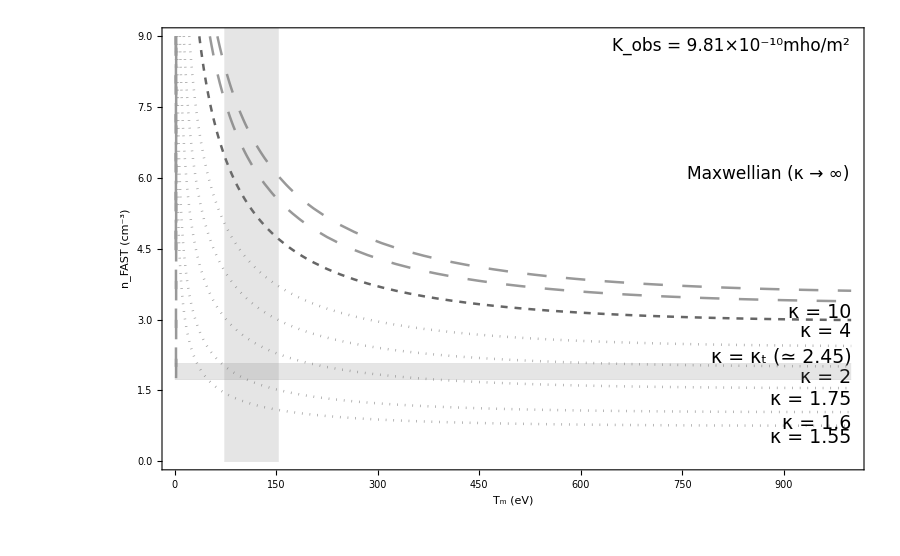

```mathematica
Show[Table[Plot[funker[Ep,Tm,kappas[[k]],measCond],{Tm,1,1000},PlotStyle->styles[[k]],PlotLegends->LineLegend[Automatic],Epilog->{Text[Style["K_obs = 9.81×10^-10mho/m^2",FontSize->17],Scaled[{0.98,0.98}],{1,1}],Text[Style["Maxwellian (κ → ∞)",FontSize->17],Scaled[{0.98,0.69}],{1,1}]},PlotRange->{{1,999},{0,5}},PlotRangeClipping->True,PlotLabels ->Placed[kappaLabels[[k]] ,placeList[[k]]],LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],{k,{1,2,3,4,5,6,7,8}}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

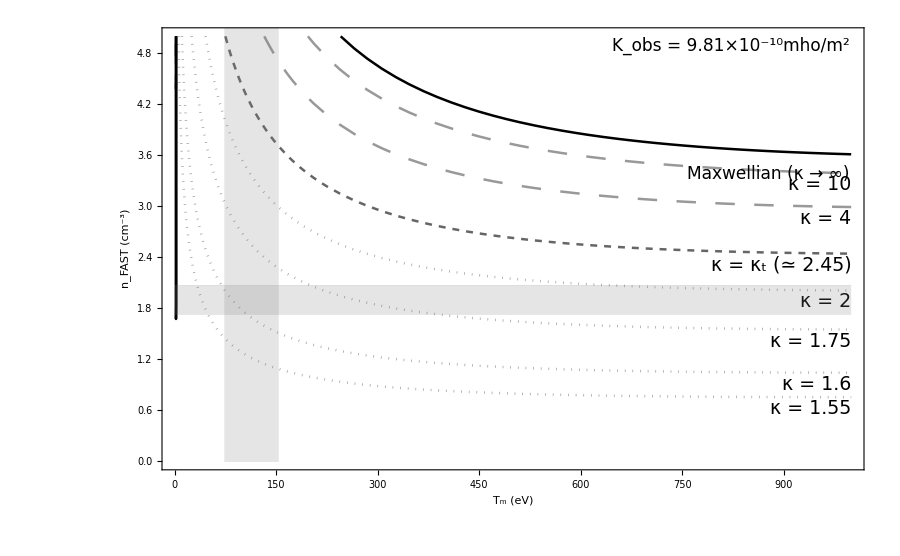

```mathematica
Show[Table[Plot[funker[Ep,Tm,kappas[[k]],measCond],{Tm,1,1000},PlotStyle->styles[[k]],PlotLegends->LineLegend[Automatic],Epilog->{Text[Style["K_obs = 9.81×10^-10mho/m^2",FontSize->17],Scaled[{0.98,0.98}],{1,1}],Text[Style["Maxwellian (κ → ∞)",FontSize->17],Scaled[{0.98,0.69}],{1,1}]},PlotRange->{{1,999},{0,5}},PlotRangeClipping->True,PlotLabels ->Placed[kappaLabels[[k]] ,placeList[[k]]],LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],{k,{1,2,3,4,5,6,7,8}}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```

### No labels, handle manually

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

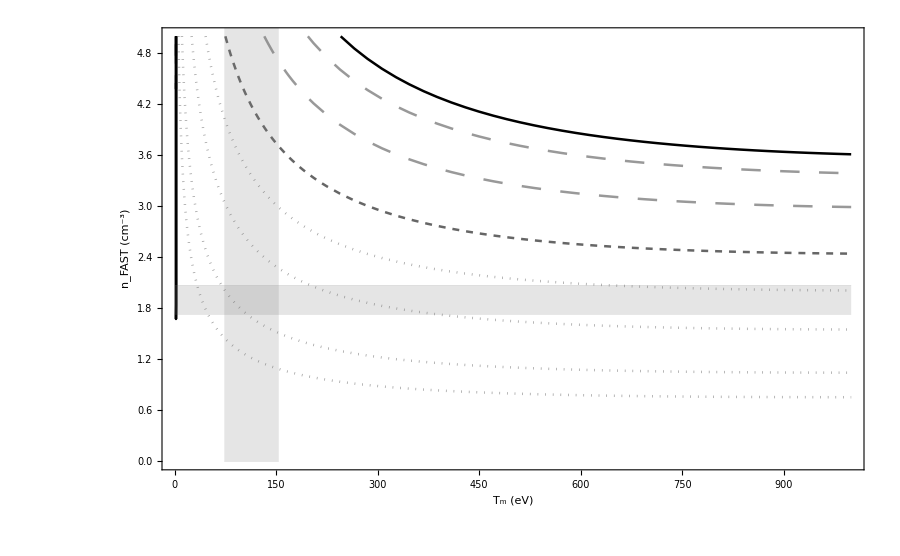

```mathematica
Show[Table[Plot[funker[Ep,Tm,kappas[[k]],measCond],{Tm,1,1000},PlotStyle->styles[[k]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,999},{0,5}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],{k,{1,2,3,4,5,6,7,8}}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```

```mathematica
CurrentValue[{StyleDefinitions,"Graphics","FontFamily"}]
```

Arial